```mathematica
Needs["PlotLegends`"]
```

```mathematica
(* MODEL PARAMETERS *)
(* - - - - - - - - - *)
Nns=5.0*10^6; (* Number of non-specific binding sites *)
P=1000;               (* Number of RNAP molecules   *)
Ermd=-17.3;     (* Operator binding energy *)
Epd=-3;                (* RNAP binding energy *)
```

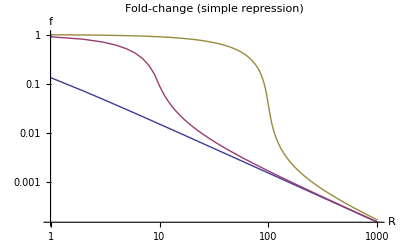

```mathematica
(* FOLD-CHANGE: SIMPLE REPRESSION *)
(* - - - - - - - - - - - - - - - - *)

(* Single promoter partition function *)
Z[0]:=1+p;        
Z[1]:= E^(-Ermd);
Z[i_]:=0;

(* Multiple promoter partition function *)
ZtotID[F_,0]=1;  
ZtotID[F_,n_]:=Sum[Multinomial[k1,n-k1]F!/(F-k1)!/Nns^k1 Z[0]^(n-k1) Z[1]^k1   ,{k1,0,Min[n,F]}];

(* Fold-change *)
f[F_,n_]:=D[Log[ZtotID[F,n]],p]/n/D[Log[ZtotID[0,1]],p] /. p->P/Nns*E^(-Epd) ;

(* Plot *)
ListLogLogPlot[{Table[{x,f[x,1]},{x,1,1000}],Table[{x,f[x,10]},{x,1,1000}],Table[{x,f[x,100]},{x,1,1000}]},Joined-> True,PlotRange-> {{1,1000},{0,10^-4}},PlotLegend-> {"N=1","N=10","N=100"},LegendPosition->{0.6,-0.39},AxesLabel-> {"R","f"},PlotLabel-> "Fold-change (simple repression)"]
```

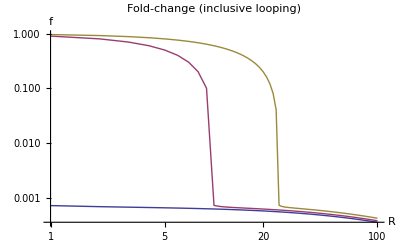

```mathematica
(* FOLD-CHANGE: INCLUSIVE LOOPING REPRESSION *)
(* - - - - - - - - - - - - - - - - - - - - -  *)

Floop=10;    (* Looping free energy *)
k=2;               (* k=2 --> both repressor heads bound *)

Z1[0]:=1+p;
Z1[1] := k Exp[-Ermd](2+p)+k Exp[-(2Ermd+Floop)];
Z1[2] :=k^2 Exp[-2Ermd];
Z1[n_] := 0;
Z[R_,n_]:= Sum[Multinomial[k2,k1,n-k1-k2] R!/Nns^(k1+2k2)/(R-k1-2k2)! Z1[0]^(n-k1-k2)*Z1[1]^k1 Z1[2]^k2,{k2,0,Min[n,Floor[R/2]]},{k1,0,Min[n-k2,R-2k2]}];

f[R_,n_]:= D[Log[Z[R,n]],p] / n/D[Log[Z[0,1]],p]  /.{ p->P/Nns*Exp[-Epd]};

ListLogLogPlot[{Table[{x,f[x,1]},{x,1,100}],Table[{x,f[x,10]},{x,1,100}],Table[{x,f[x,25]},{x,1,100}]},Joined-> True,PlotRange-> {{1,100},All},PlotLegend-> {"N=1","N=10","N=25"},LegendPosition->{0.6,-0.39},AxesLabel-> {"R","f"},PlotLabel-> "Fold-change (inclusive looping)"]
```

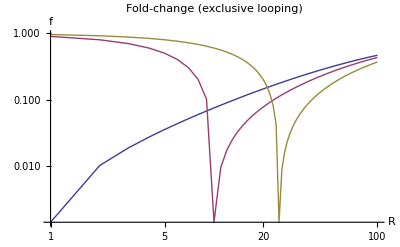

```mathematica
(* FOLD-CHANGE: EXCLUSIVE LOOPING REPRESSION *)
(* - - - - - - - - - - - - - - - - - - - - -  *)

k=2;
Floop=10;

Z1[0]:=1+p;
Z1[1] :=k Exp[-Ermd](2+2 p)+k Exp[-(2Ermd+Floop)];
Z1[2] := k^2 Exp[-2 Ermd](1+p);
Z1[n_] := 0;
Z[R_,n_]:= Sum[Multinomial[k2,k1,n-k1-k2] R!/Nns^(k1+2k2)/(R-k1-2k2)! Z1[0]^(n-k1-k2)*Z1[1]^k1 Z1[2]^k2,{k2,0,Min[n,Floor[R/2]]},{k1,0,Min[n-k2,R-2k2]}];

f[R_,n_]:= N[D[Log[Z[R,n]],p] / n/D[Log[Z[0,1]],p]  /.{ p->P/Nns*Exp[-Epd]}];

ListLogLogPlot[{Table[{x,f[x,1]},{x,1,100}],Table[{x,f[x,10]},{x,1,100}],Table[{x,f[x,25]},{x,1,100}]},Joined-> True,PlotRange-> {{1,100},All},PlotLegend-> {"N=1","N=10","N=25"},LegendPosition->{0.6,-0.39},AxesLabel-> {"R","f"},PlotLabel-> "Fold-change (exclusive looping)"]
```

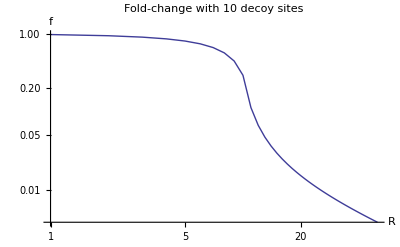

```mathematica
(* FOLD-CHANGE: SIMPLE REPRESSION WITH DECOY SITES *)
(* - - - - - - - - - - - - - - - - - - - - - - - -  *)

Epl=-18.5;    (* Binding energy of decoy site *)

Z1[Np_,i_]:=Binomial[Np,i] E^(-i Epl);
Z2[0]:=1+p;
Z2[1]:=E^(-Ermd);

Ztot[R_,Np_]=Sum[R!/Nns^(f1+f2)/(R-f1-f2)! Z1[Np,f1]Z2[f2],{f1,0,Min[Np,R]},{f2,0,Min[1,R-f1]}];
f2[R_,Np_] := D[Log[Ztot[R,Np]],p]/D[Log[Ztot[0,Np]],p] /. p->P/Nns*E^(-Epd) ;

ListLogLogPlot[Table[{i,f2[i,10]},{i,0,50}],Joined-> True,PlotRange-> {{1,50},All},AxesLabel-> {"R","f"},PlotLabel-> "Fold-change with 10 decoy sites"]
```

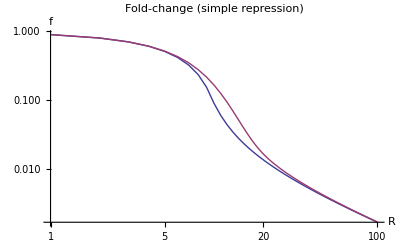

```mathematica
(* DISTRIBUTION OF PROMOTER COPY NUMBER: FOLD-CHANGE FOR SIMPLE REPRESSOR *)
(* - - - - - - - - - - - - - - - - *)

(* Single promoter partition function *)
Z[0]:=1+p;        
Z[1]:= E^(-Ermd);
Z[i_]:=0;

(* Multiple promoter partition function *)
ZtotID[F_,0]=1;  
ZtotID[F_,n_]:=Sum[Multinomial[k1,n-k1]F!/(F-k1)!/Nns^k1 Z[0]^(n-k1) Z[1]^k1   ,{k1,0,Min[n,F]}];

(* Fold-change *)
f[F_,n_,nmean_]:=D[Log[ZtotID[F,n]],p]/nmean/D[Log[ZtotID[0,1]],p] /. p->P/Nns*E^(-Epd) ;

(* Note: When considering a distribution of repressor or promoter copy numbers one might need to truncate the distribution after some number of standard deviations, for computational efficieny. *)

simprepf=Table[{i,f[i,10,10]},{i,0,100}]; (* Fold-change, fixed N. *)
simprepfPo10=Table[{i,Sum[PDF[PoissonDistribution[10],j]*f[i,j,10],{j,0,20}]},{i,0,100}]; (* Fold-change, Poisson distribution of promoter copies (mean=10) *)

ListLogLogPlot[{simprepf,simprepfPo10},Joined-> True,PlotRange-> {{1,100},All},AxesLabel-> {"R","f"},PlotLegend-> {"N=10","N=Po(10)"},LegendPosition->{0.6,-0.39},PlotLabel-> "Fold-change (simple repression)"]
```

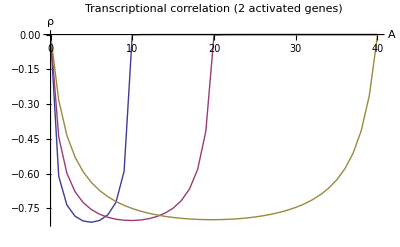

```mathematica
(* TRANSCRIPTIONAL CORRELATION: TWO ACTIVATED GENES *)
(* - - - - - - - - - - - - - - - - - - - - - - - - - *)

Eint=-7;   (* Interaction energy RNAP-TF *)
Epd=-5;

Z1[0]:=1+p1+p2+p1 p2;
Z1[1] :=Exp[-Ermd](1+Exp[-Eint] p1)(1+p2)+Exp[-Ermd](1+ p1)(1+Exp[-Eint] p2);
Z1[2] := Exp[-2Ermd] (1+Exp[-Eint] p1)(1+Exp[-Eint] p2);
Z1[n_] := 0;
Z[R_,n_]:= Sum[Multinomial[k2,k1,n-k1-k2] R!/Nns^(k1+2k2)/(R-k1-2k2)! Z1[0]^(n-k1-k2)*Z1[1]^k1 Z1[2]^k2,{k2,0,Min[n,Floor[R/2]]},{k1,0,Min[n-k2,R-2k2]}];

(* Correlation coefficient *)
ρ[R_,n_]:= p1 p2 D[Log[Z[R,n]],p1,p2] / (p2 D[Log[Z[R,n]],p2]+p2^2 D[Log[Z[R,n]],p2,p2]) /.{ p1->P/Nns*Exp[-Epd],p2->P/Nns*Exp[-Epd]};

ListPlot[{Table[{R,ρ[R,5]},{R,0,40}],Table[{R,ρ[R,10]},{R,0,40}],Table[{R,ρ[R,20]},{R,0,40}]},Joined-> True,AxesLabel-> {"A","ρ"},PlotLegend-> {"N=5","N=10","N=20"},PlotRange-> All,LegendPosition->{0.6,-0.39} ,PlotLabel-> "Transcriptional correlation (2 activated genes)"]
```